```mathematica
{1, 3, 4}
```

{1,3,4}

```mathematica
{1, a, cat, CurrentImage[]}
```

```mathematica
myList = {1,a,cat,-Graphics-}
```

{1,a,cat,-Graphics-}

```mathematica
myList + 1
```

{2,1+a,1+cat,1+-Graphics-}

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Range[3,8]
```

{3,4,5,6,7,8}

```mathematica
myList[[{3, 2}]]
```

{cat,a}

```mathematica
cat + 1
```

1+cat

```mathematica
myList[[4]]
```

-Graphics-

```mathematica
Table[i , {i, 1 }]
```

{1}

```mathematica
Table[i , {i, 1 , 8,2}]
```

{1,3,5,7}

```mathematica
Table[i , {i, 1 , 8,0.2}]
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.}

```mathematica
dicerolls = RandomInteger[{1,6}, 10]
```

{2,6,5,6,2,1,5,5,5,4}

```mathematica
1.0 * Mean[dicerolls]
```

3.50004

```mathematica
dicerolls = RandomInteger[{1,6}, 10000000];
```

```mathematica
squares = Table[i^2,{i,1,8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8 = Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[f, {a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
Map[#^2 &,upto8]
```

```mathematica
Map[Sqrt[#] &,{1,4,9,16,25,36,49,64}]
```

{1,2,3,4,5,6,7,8}

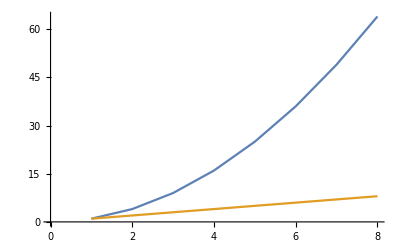

```mathematica
ListPlot[{squares,upto8}, Joined->True]
```

```mathematica
Length[squares]
```

8

```mathematica
NestList[f,a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

```mathematica
NestList[#*2 &, 1, 5]
```

{1,2,4,8,16,32}

```mathematica
NestWhileList[#*2 &, 1, # ≤ 129 &]
```

{1,2,4,8,16,32,64,128,256}

```mathematica
{1,2,3} + {a,b,c}
```

{1+a,2+b,3+c}

```mathematica
{1,2,3} + 1
```

{2,3,4}

```mathematica
Union[{1,2,3},{3,4}]
```

{1,2,3,4}

```mathematica
Intersection[{1,2,3} , {3,4,5}]
```

{3}

```mathematica
Subsets[{1,2,3,4}]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
Join[{1,2,4,3},{1,2,9,1}]
```

{1,2,4,3,1,2,9,1}

```mathematica
Riffle[{1,2},{a,b}]
```

{1,a,2,b}

```mathematica
Range[10]
```

```mathematica
Take[{1,2,3,4,5,6,7,8,9,10}, 3]
```

{1,2,3}

```mathematica
Drop[{1,2,3,4,5,6,7,8,9,10}, 3]
```

{4,5,6,7,8,9,10}

```mathematica
NestList[Riffle[Take[#,5],Drop[#,5]] &, {1,2,3,4,5,6,7,8,9,10},10]
```

{{1,2,3,4,5,6,7,8,9,10},{1,6,2,7,3,8,4,9,5,10},{1,8,6,4,2,9,7,5,3,10},{1,9,8,7,6,5,4,3,2,10},{1,5,9,4,8,3,7,2,6,10},{1,3,5,7,9,2,4,6,8,10},{1,2,3,4,5,6,7,8,9,10},{1,6,2,7,3,8,4,9,5,10},{1,8,6,4,2,9,7,5,3,10},{1,9,8,7,6,5,4,3,2,10},{1,5,9,4,8,3,7,2,6,10}}

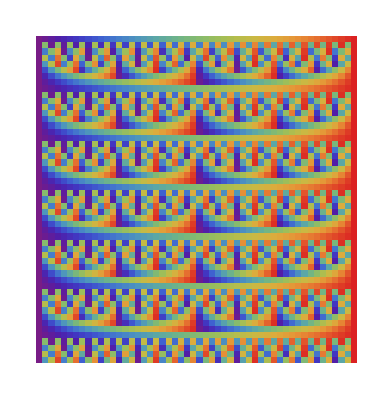

```mathematica
ArrayPlot[NestList[Riffle[Take[#,26],Drop[#,26]] &, Range[52],52],ColorFunction->"Rainbow"]
```

```mathematica
{{1,2,3},{1,2,3}}
```

{{1,2,3},{1,2,3}}

```mathematica
MatrixForm[{{1,2,3},{1,2,3}}]
```

(1 | 2 | 3
1 | 2 | 3)

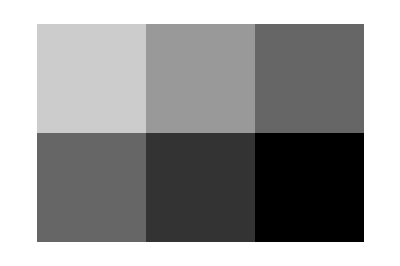

```mathematica
ArrayPlot[{{1,2,3},{3,4,5}}]
```

```mathematica
Sqrt[4]
```

2

```mathematica
timestwoadd[varx_]:= 2*varx + 1
```

```mathematica
timestwoadd[2]
```

5

```mathematica
fn := #*2+1 &
```

```mathematica
fn[2]
```

5

```mathematica
testifinputis7[wat_] := If[wat == 7,1,0]
```

```mathematica
testifinputis7[7]
```

1

```mathematica
testifinputis7[6.99999]
```

0

```mathematica
Map[testifinputis7, Range[9]]
```

{0,0,0,0,0,0,1,0,0}

```mathematica
If[ 4 >2,1,0]
```

1

```mathematica
Map[{#,Mod[#,5]} &, Range[30]]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{6,1},{7,2},{8,3},{9,4},{10,0},{11,1},{12,2},{13,3},{14,4},{15,0},{16,1},{17,2},{18,3},{19,4},{20,0},{21,1},{22,2},{23,3},{24,4},{25,0},{26,1},{27,2},{28,3},{29,4},{30,0}}

```mathematica
Mod[21,5]
```

1

```mathematica
collatz[x_,y_] := If[x == 3*y || x == 2*y +1|| y == 3*x || y== 2*x+1,1,0]
```

```mathematica
collatz[3,9]
```

1

```mathematica
Array[#&, 10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Array[#^2 &,10]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Array[#^2 &, {4,4}]
```

{{1,1,1,1},{4,4,4,4},{9,9,9,9},{16,16,16,16}}

```mathematica
Array[#1 + 2#2 &, {4,4}]
```

{{3,5,7,9},{4,6,8,10},{5,7,9,11},{6,8,10,12}}

```mathematica
Array[collatz[#1,#2] &,{20,20}]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AdjacencyGraph[Array[collatz[#1,#2] &,{50,50}]]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraphPlot3D[AdjacencyGraph[Array[collatz[#1,#2] &,{50,50}]]]
```

-Graphics3D-

```mathematica
Map[Mod[#,7] &,Range[100]]
```

{1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2,3,4,5,6,0,1,2}

```mathematica
Position[Map[Mod[#,7] &,Range[100]],6]
```

{{6},{13},{20},{27},{34},{41},{48},{55},{62},{69},{76},{83},{90},{97}}

```mathematica
Map[#[[1]] &, Position[Map[Mod[#,7] &,Range[100]],6]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
Flatten[{{1,3,4},{2,3,4},{2,5,6}}]
```

{1,3,4,2,3,4,2,5,6}

```mathematica
Select[Table[i,{i,1,10}], Mod[#,3] ==0 &]
```

{3,6,9}

```mathematica
RandomReal[{0,1},7]
```

{0.245608,0.954477,0.717296,0.870074,0.34704,0.951086,0.615235}

```mathematica
Sort[RandomReal[{0,1},7],#1≥ #2 &]
```

{0.976608,0.708965,0.661468,0.522991,0.254065,0.163882,0.066262}

```mathematica
"mystring"
```

mystring

```mathematica
StringJoin["dog", "cat", "Fish"]
```

dogcatFish

```mathematica
Stra = ToString[{6,13,20,27,34,41,48,55,62,69,76,83,90,97}]
```

{6, 13, 20, 27, 34, 41, 48, 55, 62, 69, 76, 83, 90, 97}

```mathematica
StringJoin[Stra, "dog"]
```

{6, 13, 20, 27, 34, 41, 48, 55, 62, 69, 76, 83, 90, 97}dog

```mathematica
ToExpression[{6,13,20,27,34,41,48,55,62,69,76,83,90,97}]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
StringSplit[{6,13,20,27,34,41,48,55,62,69,76,83,90,97},"1"]
```

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{6,13,20,27,34,41,48,55,62,69,76,83,90,97},1].

```mathematica
StringSplit["{6,13,20,27,34,41,48,55,62,69,76,83,90,97}","1"]
```

{{6,,3,20,27,34,4,,48,55,62,69,76,83,90,97}}

```mathematica
StringReplace["{6,13,20,27,34,41,48,55,62,69,76,83,90,97}","1"-> "10"]
```

{6,103,20,27,34,410,48,55,62,69,76,83,90,97}

```mathematica
Characters["Catfish"]
```

{C,a,t,f,i,s,h}

```mathematica
NestList[StringReplace[#, "110" ->"100011101"] &, "110110110", 5]
```

{110110110,100011101100011101100011101,100011000111011000111010011000111011000111010011000111011,100010001110100110001110110001110100110001110110010001110100110001110110001110100110001110110010001110100110001110111,100010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101100011101001100011101100100011101001100011101100011101010001100011101100100011101001100011101111,100010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011001000111010011000111011000111010100011000111011001000111010011000111011000111010011000111011010001000111010011000111011000111010100011000111011001000111010011000111011111}

```mathematica
conv[x_] := Map[If[# == "0",1,2]&,Characters[x]]
```

```mathematica
conv["11010101"]
```

{2,2,1,2,1,2,1,2}

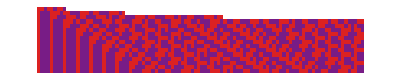

```mathematica
ArrayPlot[Map[Take[conv[#],Min[100,StringLength[#]]] &,NestList[StringReplace[#, "110" ->"100011101"] &, "110110110", 15]], ColorFunction->"Rainbow"]
```

```mathematica
cat = 7
```

7

```mathematica
cat
```

7

```mathematica
Module[{dog = 9,cat=5}, dog+cat]
```

14

```mathematica
dog
```

```mathematica
dog
cat
```

dog

7

```mathematica
cat
```

7

```mathematica
Module[{Sqrt=9},Sqrt+1]
```

10

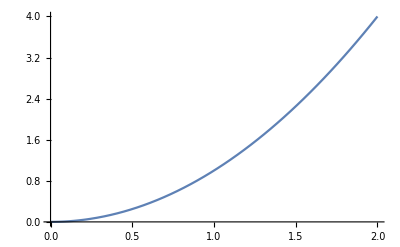

```mathematica
Plot[x^2,{x,0,2}]
```

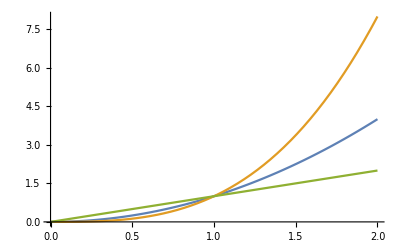

```mathematica
Plot[{x^2,x^3,x},{x,0,2}]
```

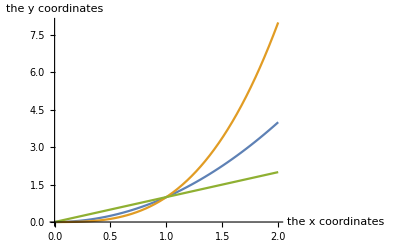

```mathematica
Plot[{x^2,x^3,x},{x,0,2}, AxesLabel->{"the x coordinates","the y coordinates"}]
```